## Startup

```mathematica
<<madtomma`madinput`madinput`
```

SetDelayed::write: Tag FindPeaks in FindPeaks[data1_,data2_,Opts___] is Protected.

```mathematica
<<madtomma`madinput`readinmadfiles2`
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\jkj62\Documents\GitHub\CBETA

```mathematica
??RunMAD
```

RunMAD[Filename]
RunMAD is used to run the MAD program on a selected input file

RunMAD[Madtomma`MADInput`MADInput`Private`file_]:=Block[{},If[DirectoryName[Madtomma`MADInput`MADInput`Private`file]===,Import[!<>c:\MAD8dl\mad8dl.bat <>Madtomma`MADInput`MADInput`Private`getShortDirectory[]<>\<>ToString[Madtomma`MADInput`MADInput`Private`file],String];,Import[!<>c:\MAD8dl\mad8dl.bat <>ToString[Madtomma`MADInput`MADInput`Private`file],String]];Return[]]

```mathematica
ReadInMADFile["MERGEr_sb_4q.MFF"]
```

matrix

matrix

matrix

«1 more identical outputs»

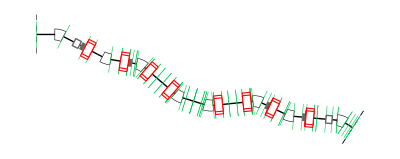

```mathematica
LAT//MADDraw
```

betax, alphax, betay, alphay, dx, dpx

```mathematica
beta0={12.64088207,1.01120776,12.64081668,0.76108300,-0.00130348,-0.03720360}
```

{12.6409,1.01121,12.6408,0.761083,-0.00130348,-0.0372036}

```mathematica
Select[MADFlatten[LAT],#[[2]]==="Quadrupole"&&#[[3]]>0.1&]
```

{{S1$PIP02$MS1019,Quadrupole,0.2,0.,---,---,},{S1$PIP03$MS1020,Quadrupole,0.2,0.,---,---,},{S1$PIP04$MS1022,Quadrupole,0.2,8.76736,---,---,},{S1$PIP05$MS1023,Quadrupole,0.2,-12.9025,---,---,},{S1$PIP08$MS1024,Quadrupole,0.2,-0.744,---,---,},{S1$PIP09$MS1025,Quadrupole,0.2,4.84283,---,---,},{S1$PIP10$MS1028,Quadrupole,0.193,0.,---,---,},{S1$PIP11$MS1031,Quadrupole,0.193,0.,---,---,}}

ToExpression[#[[1, 1]] <> "[[1,4]]=" <> ToString[NumberRight[#[[2]]]]] & /@ Transpose[{Union[Select[MADFlatten[LAT], #[[2]] === "Quadrupole" && #[[3]] > 0.1 &]], {0, 0, -1.22827937173736212, 1.80760392469078401, 0.104232064439637784, -0.678466056731410028, 0, 0}}]

{0.,0.,-1.22828,1.8076,0.104232,-0.678466,0.,0.}

```mathematica
MADWrite["merge",LAT,Slice->1];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
```

```mathematica
mfsInterpret["optics.txt"]
```

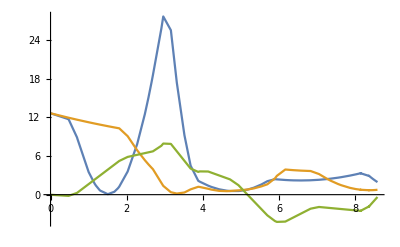

```mathematica
ListLinePlot[{Transpose[{S,BETX}],Transpose[{S,BETY}],Transpose[{S,10 DX}]},PlotRange->All]
```

```mathematica
baseTwiss
```

{2.60648,0.242099,2.67246,-2.45725,-0.0365053,0.662909}

```mathematica
baseTwiss
```

{2.60648,0.242099,2.67246,-2.45725,-0.0365053,0.662909}

```mathematica
getTwiss[]:={BETX,ALFX,BETY,ALFY,DX,DPX}[[All,-1]]
```

```mathematica
Unprotect[baseTwiss]
```

{baseTwiss}

```mathematica
baseTwiss=getTwiss[]
Protect[baseTwiss];
```

{1.95038,1.91241,0.758206,-0.317298,-0.0365053,0.662909}

```mathematica
quads=Union[Select[MADFlatten[LAT],#[[2]]==="Quadrupole"&&#[[3]]>0.1&]][[3;;-3]]
```

{{S1$PIP04$MS1022,Quadrupole,0.2,8.76736,---,---,},{S1$PIP05$MS1023,Quadrupole,0.2,-12.9025,---,---,},{S1$PIP08$MS1024,Quadrupole,0.2,-0.744,---,---,},{S1$PIP09$MS1025,Quadrupole,0.2,4.84283,---,---,}}

```mathematica
Brho=QuantityMagnitude[UnitConvert[Quantity[42,"MeV/c"]/Quantity["ElementaryCharge"],"Tesla Meter"]]
```

0.1400969

```mathematica
q4settings=-{-1.22827937173736212, 1.80760392469078401,0.1*1.04232064439637784,0.1*-6.78466056731410028}/Brho
```

{8.767355,-12.90252,-0.744,4.84283}

```mathematica
startK=#[[4]]&/@quads
```

{8.76736,-12.9025,-0.744,4.84283}

```mathematica
gradient[data_]:=Block[{k},
k=data[[All,1]];
Coefficient[Fit[Transpose[{k,#}],{1,fitvar},fitvar],fitvar]&/@Rest[Transpose[data]]
]
```

## Try 1

```mathematica
matFunc[quad_,k_]:=Block[{startK},
startK=ToExpression[quad[[1]]][[1,4]];
ToExpression[quad[[1]]<>"[[1,4]]="<>ToString[NumberRight[k]]];
MADWrite["merge",LAT,Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
ToExpression[quad[[1]]<>"[[1,4]]="<>ToString[NumberRight[startK]]];
Join[{k},baseTwiss-getTwiss[]]
]
```

```mathematica
getMatrixData[]:=Block[{quad=#[[1]],startK=#[[2]]},
testdata=matFunc[quad,#+startK]&/@Range[-0.1,0.1,0.1];
gradient[testdata]/baseTwiss]&/@Transpose[{quads,startK}]
```

```mathematica
startK
```

{8.76736,-12.9025,-0.744,4.84283}

```mathematica
rmdata=getMatrixData[]
```

{{1.7572,-1.05317,-0.0669739,-0.495386,5.21205,-0.642253},{0.0949302,-0.214389,-0.177762,0.231565,0.375576,-0.115016},{-0.0361724,0.0302759,0.143312,0.0813588,-0.356962,-0.0212774},{0.367467,0.514639,0.148654,1.30819,3.88523,0.155572}}

```mathematica
testKnobs[knobValues_]:=Block[{},
ToExpression[#[[1]][[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,knobValues}];
MADWrite["merge",LAT,Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
ToExpression[#[[1]][[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,startK}];
baseTwiss-getTwiss[]
]
```

```mathematica
Clear[singularValuesDecompositionInverse];
singularValuesDecompositionInverse[list_,n_:All,αin_:0]:=Block[{α=If[αin===0||αin===0.,10^-12,αin]},
{u,w,v}=SingularValueDecomposition[list,n];
(*winv= SparseArray[{i_, i_}:>1/w[[i,i]],Length[w]];*)
winv=SparseArray[{i_, i_}:>w[[i,i]]^1/(w[[i,i]]^2+α^2),Length[w]];
v.winv.ConjugateTranspose[u]
(*PseudoInverse[list,Tolerance->n]*)
]
```

```mathematica
knob[str_,array_]:=startK+str (Transpose[singularValuesDecompositionInverse[rmdata,3,1]].(array/baseTwiss))
```

```mathematica
#/Max[#]&[knob[1,{1,0,0,0,0,0}]-startK]
```

{1.,-0.0233616,-0.049978,-0.89735}

```mathematica
knob[1,{1,0,0,0,0,0}]-startK
```

{0.0580527,-0.00135621,-0.00290136,-0.0520936}

```mathematica
startK
```

{8.76736,-12.9025,-0.744,4.84283}

```mathematica
knob[1,(Transpose[rmdata].startK)]-startK
```

{-142.858,32.9545,8.62747,-198.144}

```mathematica
quads[[All,1]]
```

{S1$PIP04$MS1022,S1$PIP05$MS1023,S1$PIP08$MS1024,S1$PIP09$MS1025}

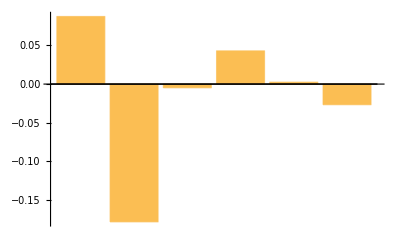

```mathematica
testKnobs[knob[0.1,{0,0,0,1,0,0}]]//BarChart
```

## Try 2

```mathematica
matFunc[quad_,k_]:=Block[{startK},
startK=ToExpression[quad[[1]]][[1,4]];
ToExpression[quad[[1]]<>"[[1,4]]="<>ToString[NumberRight[k]]];
MADWrite["merge",LAT,Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
ToExpression[quad[[1]]<>"[[1,4]]="<>ToString[NumberRight[startK]]];
Join[{k},baseTwiss-getTwiss[]]
]
```

```mathematica
getMatrixData[]:=Block[{quad=#[[1]],startK=#[[2]]},
testdata=matFunc[quad,#+startK]&/@{0.001,0.001,0.001};
gradient[testdata]/(0.001 baseTwiss)]&/@Transpose[{quads,startK}]
```

```mathematica
testdata
```

{{6.65918,0.,0.,0.,0.,0.,0.},{6.65918,0.,0.,0.,0.,0.,0.},{6.65918,0.,0.,0.,0.,0.,0.}}

```mathematica
startK
```

{1.56954,-10.8659,11.0137,-12.6049,-13.0748,10.9554,-13.0516,-13.0516,6.65818,6.65818}

```mathematica
rmdata=getMatrixData[]
```

{{-0.161464,-3.81237,-0.349215,3.0994,0.616949,-0.351124},{-0.0309847,-0.441253,0.0428385,-0.236498,-0.334506,-0.0967067},{0.436912,7.47975,-0.0118696,0.155038,1.7512,0.770699},{-0.0273587,-0.266039,0.524771,-3.4075,-0.283598,-0.123175},{0.0233431,0.452638,0.472359,-3.20507,-0.0677463,-0.0770188},{-0.055881,0.0926727,-0.00715968,0.0731973,-0.0711138,0.333341},{0.0212149,0.455849,-0.013374,0.0470822,-0.0808787,-0.011225},{0.0225167,0.311742,0.0394207,-0.405091,-0.0492416,-0.0468354},{-0.0398759,-0.873457,0.0276827,-0.111445,0.155005,0.0182058},{0.,0.,0.,0.,0.,0.}}

```mathematica
testKnobs[knobValues_]:=Block[{},
ToExpression[#[[1]][[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,knobValues}];
MADWrite["merge",LAT,Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
ToExpression[#[[1]][[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,startK}];
baseTwiss-getTwiss[]
]
```

```mathematica
Clear[singularValuesDecompositionInverse];
singularValuesDecompositionInverse[list_,n_:All,αin_:0]:=Block[{α=If[αin===0||αin===0.,10^-12,αin]},
{u,w,v}=SingularValueDecomposition[list,n];
(*winv= SparseArray[{i_, i_}:>1/w[[i,i]],Length[w]];*)
winv=SparseArray[{i_, i_}:>w[[i,i]]^1/(w[[i,i]]^2+α^2),Length[w]];
v.winv.ConjugateTranspose[u]
(*PseudoInverse[list,Tolerance->n]*)
]
```

```mathematica
knob[str_,array_]:=startK+str (Transpose[singularValuesDecompositionInverse[rmdata,4,1]].(baseTwiss*array))
```

```mathematica
#/Max[#]&[knob[1,{1,0,0,0,0,0}]-startK]
```

{1.,0.220083,0.871988,0.184031,0.629893,-3.37867,0.472207,0.663067,-0.873919,0.}

```mathematica
knob[1,{1,0,0,0,0,0}]-startK
```

{0.00109701,0.000241433,0.000956579,0.000201883,0.000690998,-0.00370643,0.000518015,0.00072739,-0.000958697,0.}

```mathematica
startK
```

{1.56954,-10.8659,11.0137,-12.6049,-13.0748,10.9554,-13.0516,-13.0516,6.65818,6.65818}

```mathematica
knob[1,(Transpose[rmdata].startK)]-startK
```

{-1.76129,0.270357,0.227964,0.724313,0.728739,-0.413151,0.241159,0.273629,-0.454478,0.}

```mathematica
quads[[All,1]]
```

{S1$PIP02$MS1019,S1$PIP03$MS1020,S1$PIP04$MS1022,S1$PIP05$MS1023,S1$PIP08$MS1024,S1$PIP09$MS1025,S1$PIP10$MS1027,S1$PIP10$MS1028,S1$PIP11$MS1030,S1$PIP11$MS1031}

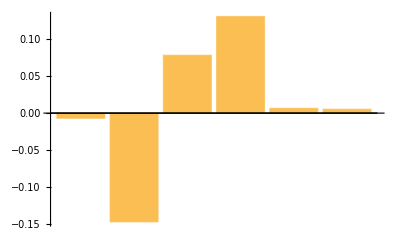

```mathematica
testKnobs[knob[1,{0,0,0,0,0,1}]]//BarChart
```

## Optimiser

```mathematica
testKnob[knobValues_, n_:1]:=Block[{},
Close[#]&/@Drop[Streams[],2];
ToExpression[#[[1]][[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,knobValues}];
MADWrite["merge",LAT,Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
ToExpression[#[[1]][[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,startK}];
(1+(100((0.1-#[[n]])^2&[baseTwiss-getTwiss[]])))/Min[Abs[(#[[n]])/Drop[#,{n}]&[baseTwiss-getTwiss[]]]]^2
]
```

```mathematica
testKnob[knob[1,{0,1,0,0,0,0}],2]
```

2.87611

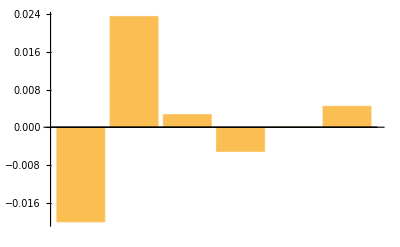

```mathematica
testKnobs[knob[0.1,{0,1,0,0,0,0}]]//BarChart
```

```mathematica
optFunc[quadvalues_,n_:1]:=Block[{},
Total[testKnob[startK+#(quadvalues-startK),n]&/@{0.01,0.1,1}]
]
```

```mathematica
knob[1,{0,1,0,0,0,0}]
```

{8.70168,-12.9889,-0.738904,4.93623}

```mathematica
optFunc[knob[0.1,{0,1,0,0,0,0}],2]
```

151.709

```mathematica
<<optimise`simplexoptimise`
```

```mathematica
ReplacePart[Table[0,6],3->1]
```

{0,0,1,0,0,0}

```mathematica
knobBETX={8.980754880685652,-12.847489573238756,-0.7247660435344463,4.970891448790605}(*{8.802364602192585,-12.968023146064983,-0.7352676722527669,4.865728170022661}*)
```

{8.98075,-12.8475,-0.724766,4.97089}

```mathematica
knobALFX={8.799698866625466,-12.780747772559712,-0.6779098042955145,4.744158385716528}(*{8.768143885785923,-13.0474852101969,-0.7260293317515938,4.88221843762226};*)
```

```mathematica
knobBETY={}(*{8.76618482094782,-12.897922220853975,-0.7891261580189975,4.8478889497082935}*)
```

{8.76618,-12.8979,-0.789126,4.84789}

```mathematica
knobALFY={}(*{8.806365403182463,-13.28676207696305,-0.7284449233421313,4.7644165403315135};*)
```

```mathematica
knobDX={}(*{8.767655091014705,-13.005353619824895,-0.912384693507484,4.580609165362897}*)
```

{8.76766,-13.0054,-0.912385,4.58061}

```mathematica
(knobBETX-startK)
```

{0.0350046,-0.0655231,0.00873233,0.0228982}

```mathematica
#/(Max[#]-Min[#])&[(knobALFX-startK)]
```

{0.00425162,-0.786366,0.0974687,0.213634}

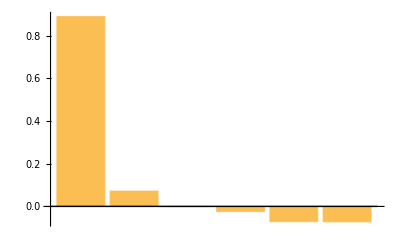

```mathematica
testKnobs[startK+1(knobBETX-startK)]//BarChart
```

```mathematica
n=1;
startsimplex=knob[0.1,ReplacePart[Table[0,6],n->1]]
```

{8.77317,-12.9026,-0.74429,4.83762}

```mathematica
n=3;
simplexans=knob[0.1,ReplacePart[Table[0,6],n->1]];
{simplexfit,simplexans}=SimplexOptimise3[Length[simplexans],{0.8,1.2}#&/@startsimplex,100,optFunc[#,n]&,StartSimplex->simplexans]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

$Aborted

```mathematica
{simplexfit,simplexans}=SimplexOptimise3[Length[simplexans],{0.99,1.01}#&/@simplexans,100,(optFunc[#,n]&),StartSimplex->simplexans]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

Power::infy: Infinite expression 1/0. encountered.

run out

Minimum Fitness: 8.65807	Raw Value: {8.83124,-13.5278,-0.773075,4.80488}	Total No. Iterations: 173	Number Restarts = 1

{8.65807,{8.83124,-13.5278,-0.773075,4.80488}}

```mathematica
n=5;
simplexans=knob[0.1,ReplacePart[Table[0,6],n->1]];
{simplexfit,simplexans}=SimplexOptimise3[10,{0.8,1.2}#&/@startsimplex,100,optFunc[#,n]&,StartSimplex->simplexans]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

run out

Minimum Fitness: 2.26929	Raw Value: {1.89812,-10.931,10.9888,-12.672,-13.0705,11.0669,-12.332,-12.9405,6.70612,7.13428}	Total No. Iterations: 247	Number Restarts = 1

{2.26929,{1.89812,-10.931,10.9888,-12.672,-13.0705,11.0669,-12.332,-12.9405,6.70612,7.13428}}

```mathematica
{simplexfit,simplexans}=SimplexOptimise3[10,{0.9,1.1}#&/@simplexans,100,(optFunc[#,n]&),StartSimplex->simplexans]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

Minimum Fitness: 2.15035	Raw Value: {1.8933,-10.922,10.9886,-12.6693,-13.0715,11.0379,-12.4648,-12.9374,6.71051,7.15014}	Total No. Iterations: 98	Number Restarts = 1

{2.15035,{1.8933,-10.922,10.9886,-12.6693,-13.0715,11.0379,-12.4648,-12.9374,6.71051,7.15014}}

```mathematica
n=6;
startsimplex=knob[0.1,ReplacePart[Table[0,6],n->1]];
{simplexfit,simplexans}=SimplexOptimise3[10,{0.8,1.2}#&/@startsimplex,100,optFunc[#,n]&,StartSimplex->startsimplex]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

Minimum Fitness: 0.488125	Raw Value: {1.93536,-10.9295,11.0524,-12.6221,-13.1089,10.272,-13.0792,-12.8332,7.48131,6.99386}	Total No. Iterations: 250	Number Restarts = 1

{0.488125,{1.93536,-10.9295,11.0524,-12.6221,-13.1089,10.272,-13.0792,-12.8332,7.48131,6.99386}}

```mathematica
{simplexfit,simplexans}=SimplexOptimise3[10,{0.9,1.1}#&/@simplexans,100,(optFunc[#,n]&),StartSimplex->simplexans,CompressionFactor->1.2,ExpansionFactor->1.2]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

run out

Minimum Fitness: 0.370618	Raw Value: {1.84887,-10.8716,11.042,-12.6036,-13.1192,10.2928,-12.6915,-12.8739,7.25007,6.99438}	Total No. Iterations: 176	Number Restarts = 1

{0.370618,{1.84887,-10.8716,11.042,-12.6036,-13.1192,10.2928,-12.6915,-12.8739,7.25007,6.99438}}

```mathematica
SimplexFinish[]
```

False

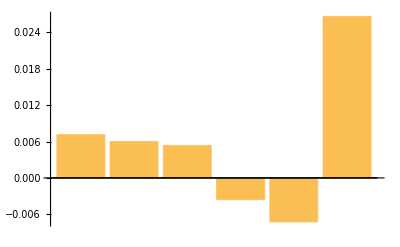

```mathematica
testKnobs[startK+0.1(simplexans-startK)]//BarChart
```

# Dipoles

## Startup

```mathematica
<<madtomma`madinput`madinput`
```

SetDelayed::write: Tag FindPeaks in FindPeaks[data1_,data2_,Opts___] is Protected.

```mathematica
<<madtomma`madinput`readinmadfiles2`
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\jkj62\Documents\GitHub\CBETA

```mathematica
??RunMAD
```

RunMAD[Filename]
RunMAD is used to run the MAD program on a selected input file

RunMAD[Madtomma`MADInput`MADInput`Private`file_]:=Block[{},If[DirectoryName[Madtomma`MADInput`MADInput`Private`file]===,Import[!<>c:\MAD8dl\mad8dl.bat <>Madtomma`MADInput`MADInput`Private`getShortDirectory[]<>\<>ToString[Madtomma`MADInput`MADInput`Private`file],String];,Import[!<>c:\MAD8dl\mad8dl.bat <>ToString[Madtomma`MADInput`MADInput`Private`file],String]];Return[]]

```mathematica
ReadInMADFile["MERGEr_sb_4q.MFF"]
```

```mathematica
LAT//MADDraw
```

matrix

matrix

matrix

«1 more identical outputs»

-Graphics-

betax, alphax, betay, alphay, dx, dpx

```mathematica
beta0={12.64088207,-1.01120776,12.64081668,-0.76108300,-0.00130348,-0.03720360}
```

{12.6409,-1.01121,12.6408,-0.761083,-0.00130348,-0.0372036}

```mathematica
Select[MADFlatten[LAT],#[[2]]==="Quadrupole"&&#[[3]]>0.1&]
```

{{S1$PIP02$MS1019,Quadrupole,0.2,0.,---,---,},{S1$PIP03$MS1020,Quadrupole,0.2,0.,---,---,},{S1$PIP04$MS1022,Quadrupole,0.2,8.76736,---,---,},{S1$PIP05$MS1023,Quadrupole,0.2,-12.9025,---,---,},{S1$PIP08$MS1024,Quadrupole,0.2,-0.744,---,---,},{S1$PIP09$MS1025,Quadrupole,0.2,4.84283,---,---,},{S1$PIP10$MS1028,Quadrupole,0.193,0.,---,---,},{S1$PIP11$MS1031,Quadrupole,0.193,0.,---,---,}}

ToExpression[#[[1, 1]] <> "[[1,4]]=" <> ToString[NumberRight[#[[2]]]]] & /@ Transpose[{Union[Select[MADFlatten[LAT], #[[2]] === "Quadrupole" && #[[3]] > 0.1 &]], {0, 0, -1.22827937173736212, 1.80760392469078401, 0.104232064439637784, -0.678466056731410028, 0, 0}}]

{0.,0.,-1.22828,1.8076,0.104232,-0.678466,0.,0.}

```mathematica
MADWrite["merge",LAT,Slice->1];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
```

```mathematica
mfsInterpret["optics.txt"]
```

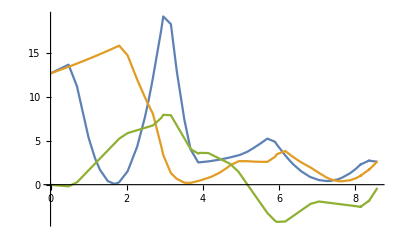

```mathematica
ListLinePlot[{Transpose[{S,BETX}],Transpose[{S,BETY}],Transpose[{S,10 DX}]},PlotRange->All]
```

```mathematica
baseTwiss
```

{2.60648,0.242099,2.67246,-2.45725,-0.0365053,0.662909}

```mathematica
getTwiss[]:={BETX,ALFX,BETY,ALFY,DX,DPX}[[All,-1]]
```

```mathematica
Unprotect[baseTwiss]
```

{baseTwiss}

```mathematica
baseTwiss=getTwiss[]
Protect[baseTwiss];
```

{2.60648,0.242099,2.67246,-2.45725,-0.0365053,0.662909}

```mathematica
dipoles=Union[Select[MADFlatten[LAT],#[[2]]==="SectorBend"&&#[[3]]>0.1&]][[3;;-3]]
```

{{MS1DIP04,SectorBend,0.221219,0.,---,-0.40633,},{MS1DIP05,SectorBend,0.221219,0.,---,-0.40633,},{MS1DIP06,SectorBend,0.221426,0.,---,0.544535,},{MS1DIP07,SectorBend,0.220846,0.,---,-0.353218,}}

```mathematica
vdipoles=Union[Select[MADFlatten[LAT],#[[2]]==="Kicker"&&#[[3]]>0.0&]][[3;;4]]
```

{{S1$PIP10$MS1026,Kicker,0.0869997,---,0.,0.,OPTICS},{S1$PIP11$MS1029,Kicker,0.087,---,0.,0.,OPTICS}}

```mathematica
hdipoles=Union[Select[MADFlatten[LAT],#[[2]]==="SectorBend"&&#[[3]]>0.0&]][[-2;;-1]]
```

{{MS1DPB01,SectorBend,0.222853,0,---,0.48,},{MS1DPB08,SectorBend,0.222853,0.,---,0.48,}}

```mathematica
Brho=QuantityMagnitude[UnitConvert[Quantity[42,"MeV/c"]/Quantity["ElementaryCharge"],"Tesla Meter"]]
```

0.1400969

```mathematica
q4settings=-{-1.22827937173736212, 1.80760392469078401,0.1*1.04232064439637784,0.1*-6.78466056731410028}/Brho
```

{8.767355,-12.90252,-0.744,4.84283}

```mathematica
startK=#[[4]]&/@quads
```

{8.76736,-12.9025,-0.744,4.84283}

```mathematica
gradient[data_]:=Block[{k},
k=data[[All,1]];
Coefficient[Fit[Transpose[{k,#}],{1,fitvar},fitvar],fitvar]&/@Rest[Transpose[data]]
]
```

```mathematica
matFuncH[kicker_,k_]:=Block[{startK},
startK=ToExpression[kicker[[1]]][[1,6]];
MADWrite["merge",LAT];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,error,"<>kicker[[1]]<>"
efield,dbl="<>ToString[NumberRight[k]]<>"\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,x,y,px,py\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
Join[{X,PX,Y,PY}[[All,-1]]]
]
```

```mathematica
matFuncV[kicker_,k_]:=Block[{startK},
startK=ToExpression[kicker[[1]]][[1,5]];
ToExpression[kicker[[1]]<>"[[1,5]]="<>ToString[NumberRight[startK+k]]];
MADWrite["merge",LAT];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,x,y,px,py\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
ToExpression[kicker[[1]]<>"[[1,5]]="<>ToString[NumberRight[startK]]];
Join[{X,PX,Y,PY}[[All,-1]]]
]
```

```mathematica
Directory[]
```

C:\Users\jkj62\Documents\GitHub\CBETA

```mathematica
vrmat=matFuncV[#,0.0001]&/@vdipoles
```

{{-9.32189×10^-6,-0.0000245457,0.170231,0.0664112},{-7.80647×10^-6,-9.78474×10^-6,0.127799,0.1}}

```mathematica
hrmat=matFuncH[#,0.0001]&/@hdipoles
```

{{-0.0130938,-0.220736,0.,0.},{-0.0320681,-0.096204,0.,0.}}

```mathematica
0.0001PseudoInverse[Transpose[vrmat]].{0,0,1,0}
```

{0.00117153,-0.00077803}

```mathematica
testKnobsV[knobValues_]:=Block[{},
ToExpression[#[[1]][[1]]<>"[[1,5]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{vdipoles,knobValues}];
MADWrite["merge",LAT,Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,x,y,px,py\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
ToExpression[#[[1]][[1]]<>"[[1,5]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{vdipoles,{0,0}}];
Join[{X,PX,Y,PY}[[All,-1]]]
]
```

```mathematica
testKnobsHV[knobValuesH_,knobValuesV_]:=Block[{},
ToExpression[#[[1]][[1]]<>"[[1,5]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{vdipoles,knobValuesV}];
MADWrite["merge",LAT];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,error,"<>#[[1,1]]<>"
efield,dbl="<>ToString[NumberRight[#[[2]]]]<>"\nselect,error,clear;\n"]&/@Transpose[{hdipoles,knobValuesH}];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,x,y,px,py\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
ToExpression[#[[1]][[1]]<>"[[1,5]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{vdipoles,{0,0}}];
Join[{X,PX,Y,PY}[[All,-1]]]
]
```

```mathematica
Join[{0,0},0.0001PseudoInverse[Transpose[vrmat]].{0,0,1,0}]
```

{0,0,0.00117153,-0.00077803}

```mathematica
testKnobsV[0.0001PseudoInverse[Transpose[vrmat]].{0,0,1,0}]
```

{0.0000307367,-0.00138412,1.,-6.59278×10^-7}

```mathematica
0.0001PseudoInverse[Transpose[hrmat]].{1,0,0,0}
```

{0.0016533,-0.00379343}

```mathematica
testKnobsHV[0.0001PseudoInverse[Transpose[hrmat]].{0.01,0,0,0},0.0PseudoInverse[Transpose[vrmat]].{0,0,0.01,0}]
```

{0.0171359,0.120235,0.,0.}